```mathematica
SetDirectory[NotebookDirectory[]];
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
nb[Epi_,T_]:=1/(Exp[Epi/T]-1);
nbd1x[Epi_,T_]:=-1/T nb[Epi,T](nb[Epi,T]+1);
mf2[h_,ρ_]:=(h^2 ρ)/2;
Eq[q_,mf2_]:=√(q^2+mf2);
Epi[q_,mp2_]:=√(q^2+mp2);
Nf=2;
Nc=3;
h=6.5;
λ=20.;
ν=-490.^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=700;
F1B1thr[mp2_,mf2_,p0_,p_,q_,x_,T_,mu_]:=1/2(-nb[Epi[√(q^2+p^2-2p q x),mp2],T]/Epi[√(q^2+p^2-2p q x),mp2]*1/((ⅈ p0-mu+Epi[√(q^2+p^2-2p q x),mp2])^2-Eq[q,mf2]^2)
-(nb[Epi[√(q^2+p^2-2p q x),mp2],T]+1)/Epi[√(q^2+p^2-2p q x),mp2]*1/((ⅈ p0-mu-Epi[√(q^2+p^2-2p q x),mp2])^2-Eq[q,mf2]^2)
+nfa[mf2,q,T,mu]/Eq[q,mf2]*1/((ⅈ p0-mu-Eq[q,mf2])^2-Epi[√(q^2+p^2-2p q x),mp2]^2)
+(nff[mf2,q,T,mu]-1)/Eq[q,mf2]*1/((ⅈ p0-mu+Eq[q,mf2])^2-Epi[√(q^2+p^2-2p q x),mp2]^2));
F1B1q0thr[mp2_,mf2_,p0_,p_,q_,x_,T_,mu_]:=1/2 ⅈ (((ⅈ p0+Epi[√(p^2+q^2-2 p q x),mp2]) nb[Epi[√(p^2+q^2-2 p q x),mp2],T])/(Epi[√(p^2+q^2-2 p q x),mp2] (-mu+ⅈ p0+Epi[√(p^2+q^2-2 p q x),mp2]-Eq[q,mf2]) (-mu+ⅈ p0+Epi[√(p^2+q^2-2 p q x),mp2]+Eq[q,mf2]))-((-ⅈ p0+Epi[√(p^2+q^2-2 p q x),mp2]) (1+nb[Epi[√(p^2+q^2-2 p q x),mp2],T]))/(Epi[√(p^2+q^2-2 p q x),mp2] (mu-ⅈ p0+Epi[√(p^2+q^2-2 p q x),mp2]-Eq[q,mf2]) (mu-ⅈ p0+Epi[√(p^2+q^2-2 p q x),mp2]+Eq[q,mf2]))-((mu+Eq[q,mf2]) nfa[mf2,q,T,mu])/(Eq[q,mf2] (-Epi[√(p^2+q^2-2 p q x),mp2]^2+(mu-ⅈ p0+Eq[q,mf2])^2))+((-mu+Eq[q,mf2]) (-1+nff[mf2,q,T,mu]))/(Eq[q,mf2] (-Epi[√(p^2+q^2-2 p q x),mp2]^2+(-mu+ⅈ p0+Eq[q,mf2])^2)));
Zpsip2[mp2_,mf2_,h_,p0_,p_,T_,mu_]:=(Nf^2-1)/(2Nf)*h^2/(4 π^2)NIntegrate[p q^3 x Re[F1B1thr[mp2,mf2,p0,p,q,x,T,mu]],{q,1,2000},{x,-1,1}]+(p^2)
mfp[mp2_,mf2_,h_,p0_,p_,T_,mu_]:=(Nf^2-1)/(2Nf)*h^2/(4 π^2)√mf2 NIntegrate[q^2 Re[F1B1thr[mp2,mf2,p0,p,q,x,T,mu]],{q,1,2000},{x,-1,1}]+√mf2
Zpsi0[mp2_,mf2_,h_,p0_,p_,T_,mu_]:=(Nf^2-1)/(2Nf)*h^2/(4 π^2)NIntegrate[q^2 Re[F1B1q0thr[mp2,mf2,p0,p,q,x,T,mu]],{q,1,2000},{x,-1,1}]/p0+1
```

# Import data

```mathematica
fpidata=Transpose[Import["../../../sigma0.dat"]];
q=Table[i,{i,1,2000,10}];
mu=Flatten[Table[i*5.,{i,1,80,1}]];
```

# Z_q spatial part

```mathematica
T=10;
mpi=Flatten[Table[√(Flatten[Import["../input/T"<>ToString[T]<>"/sigma"<>ToString[i]<>".dat"]][[1]]),{i,5,400,5}]];
(*sigmapi=Interpolation[Transpose[{q,√Flatten[Import["../input/T"<>ToString[T]<>"/sigma400.dat"]]}]];*)
dataZsp2=ParallelTable[Zpsip2[mpi[[1]]^2,mf2[6.5,(fpidata[[T]][[1]])^2/2],6.5,π  T,i*10,T,5.],{i,1,200}];
(*Export["./T"<>ToString[T]<>"/Zpsi.dat",data]*)
```

```mathematica
p2=Table[(i*10),{i,1,200}];
```

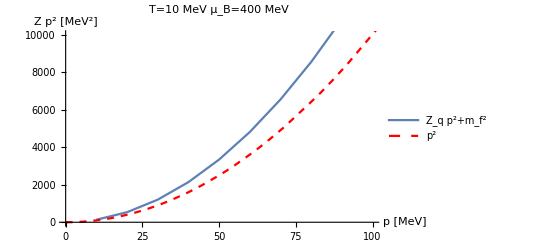

```mathematica
Show[ListLinePlot[Transpose[{p2,dataZsp2}],PlotLegends->{"Z_q p^2+m_f^2"}],Plot[x^2,{x,0,2000},PlotStyle->{Red,Dashed},PlotLegends->{"p^2"}],PlotRange->{{0,100},{0,1*10^4}},AxesLabel->{"p [MeV]","Z p^2 [MeV^2]"},PlotLabel->"T=10 MeV μ_B=400 MeV"]
```

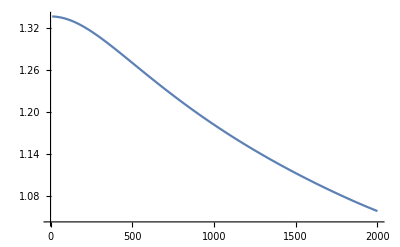

```mathematica
ListLinePlot[Transpose[{p2,dataZsp2/p2^2}]]
```

```mathematica
Export["./T10mu5/Zqs.dat",dataZsp2/p2^2]
```

./T10mu5/Zqs.dat

# m_q mass part

```mathematica
datamf=ParallelTable[mfp[mpi[[1]]^2,mf2[6.5,(fpidata[[T]][[1]])^2/2],6.5,π  T,i*10,T,5.],{i,1,200}];
```

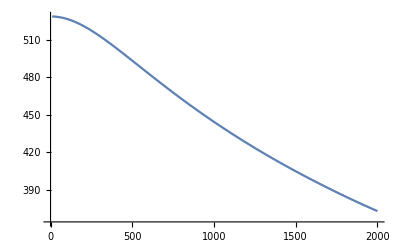

```mathematica
ListLinePlot[Transpose[{p2,datamf}]]
```

```mathematica
Export["./T10mu5/mf.dat",datamf]
```

./T10mu5/mf.dat

# Z_q temporal part

```mathematica
dataZ0=ParallelTable[Zpsi0[mpi[[1]]^2,mf2[6.5,(fpidata[[T]][[1]])^2/2],6.5,π  T,i*10,T,5.],{i,1,200}];
```

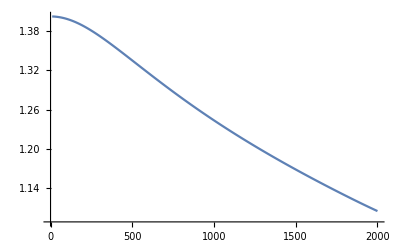

```mathematica
ListLinePlot[Transpose[{p2,dataZ0}]]
```

```mathematica
Export["./T10mu5/Zq0.dat",dataZ0]
```

./T10mu5/Zq0.dat